```mathematica
Clear[gaussian]
gaussian[x_,amplitude_,mean_,fwhm_]:=amplitude Exp[-((x-mean)^2/(2 (fwhm/(2 Sqrt[2 Log[2]]))^2))]
```

```mathematica
Clear[heaviside]
heaviside[x_,stepPosition_,amplitude_]:=amplitude UnitStep[x-stepPosition]
```

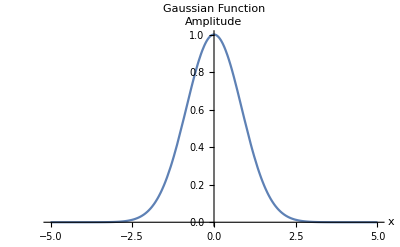

```mathematica
amplitude=1;
mean=0;
fwhm=2;

Plot[gaussian[x,amplitude,mean,fwhm],{x,-5,5},PlotRange->All,PlotLabel->"Gaussian Function",AxesLabel->{"x","Amplitude"}]
```

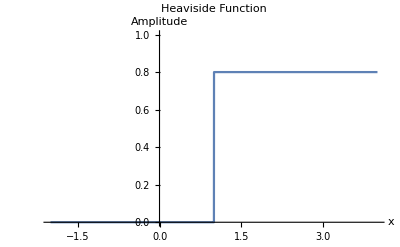

```mathematica
stepPosition=1;
amplitude=0.8;

Plot[heaviside[x,stepPosition,amplitude],{x,-2,4},PlotRange->{0,1},PlotLabel->"Heaviside Function",AxesLabel->{"x","Amplitude"}]
```

```mathematica
conv = FullSimplify[Convolve[gaussian[x,1,0,w],heaviside[x,c,a],x,y], Assumptions->{w>0,a>0}]/.y->x
```

5/2 w Erfc[(2 (c-x) √Log[2])/w] √(π/Log[2])

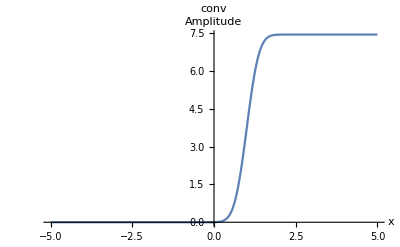

```mathematica
Plot[conv/.{w ->0.7, c->1, a -> 10},{x,-5,5},PlotRange->All,PlotLabel->"conv",AxesLabel->{"x","Amplitude"}]
```